```mathematica
Quit
```

# Modeling a two qubit system

Peter Gartin

SetDelayed::write: Tag KroneckerProduct in KroneckerProduct[args__] is Protected.

1

(λ-ω1-ω2 | -λ+ω1-ω2 | -λ-ω1+ω2 | λ+ω1+ω2
{1,0,0,0} | {0,0,1,0} | {0,1,0,0} | {0,0,0,1})

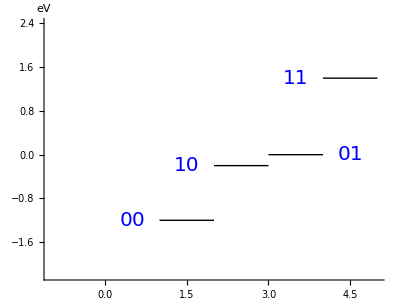

({1,3} | 2 λ-2 ω2
{1,4} | -2 ω1-2 ω2
{2,4} | -2 λ-2 ω2
{2,3} | 2 ω1-2 ω2
{1,2} | 2 λ-2 ω1
{3,4} | -2 λ-2 ω1)

```mathematica
(* Defining operations *)
Run[<<"C:\\Users\\peter\\Documents\\Research\\qi-functions\\BasicFunctions.wls"]
CircleTimes=KroneckerProduct;
Z[1]=PauliMatrix[3]⊗IdentityMatrix[2];
Z[2]= IdentityMatrix[2]⊗ PauliMatrix[3];
Z[1,2]=PauliMatrix[3]⊗ PauliMatrix[3];
(* Hamiltonian with ZZ coupling *)
Hz=-ω1 Z[1] +-ω2 Z[2]+λ Z[1,2];
(* Then energy eigenvalues are given by: *)
Eigensystem[Hz]//MatrixForm
energy=Simplify[Eigenvalues[Hz],{λ==.1,ω1==.6,ω2==.7}];
Graphics[{Inset[Style["00",20,Blue],{.5,energy[[1]]}],Inset[Style["01",20,Blue],{4.5,energy[[3]]}],Inset[Style["10",20,Blue],{1.5,energy[[2]]}],Inset[Style["11",20,Blue],{3.5,energy[[4]]}],
Table[Line[{{i,energy[[i]]},{1+i,energy[[i]]}}],{i,1,4}]},
PlotRange->{{-1,5},{Min[energy]-1,Max[energy]+1}},
Axes->{False,True},
AxesLabel->eV]
Manipulate[ {Plot[Simplify[Eigenvalues[Hz],{λ==c,ω1==a,ω2==b}],{x,-1,1},PlotRange->All],Block[{λ=c,ω1=a,ω2=b},{{{1,3},(Eigenvalues[Hz][[1]]-Eigenvalues[Hz][[3]])},
{{1,4},(Eigenvalues[Hz][[1]]-Eigenvalues[Hz][[4]])},
{{2,4},(Eigenvalues[Hz][[2]]-Eigenvalues[Hz][[4]])},
{{2,3},(Eigenvalues[Hz][[2]]-Eigenvalues[Hz][[3]])},
{{1,2},(Eigenvalues[Hz][[1]]-Eigenvalues[Hz][[2]])},
{{3,4},(Eigenvalues[Hz][[3]]-Eigenvalues[Hz][[4]])}}
]//MatrixForm},{{a,0},0,10,.01},{{b,0},0,10,.01},{{c,0},0,10,.01}]
Block[{λ,ω1,ω2},{{{1,3},(Eigenvalues[Hz][[1]]-Eigenvalues[Hz][[3]])},
{{1,4},(Eigenvalues[Hz][[1]]-Eigenvalues[Hz][[4]])},
{{2,4},(Eigenvalues[Hz][[2]]-Eigenvalues[Hz][[4]])},
{{2,3},(Eigenvalues[Hz][[2]]-Eigenvalues[Hz][[3]])},
{{1,2},(Eigenvalues[Hz][[1]]-Eigenvalues[Hz][[2]])},
{{3,4},(Eigenvalues[Hz][[3]]-Eigenvalues[Hz][[4]])}}
]//MatrixForm
```

## I repeat the process again for XX Coupling.

(-ω1-ω2 | 0 | 0 | λ
0 | -ω1+ω2 | λ | 0
0 | λ | ω1-ω2 | 0
λ | 0 | 0 | ω1+ω2)

(-√(λ^2+ω1^2-2 ω1 ω2+ω2^2) | √(λ^2+ω1^2-2 ω1 ω2+ω2^2) | -√(λ^2+ω1^2+2 ω1 ω2+ω2^2) | √(λ^2+ω1^2+2 ω1 ω2+ω2^2)
{0,-(ω1-ω2+√(λ^2+ω1^2-2 ω1 ω2+ω2^2))/λ,1,0} | {0,-(ω1-ω2-√(λ^2+ω1^2-2 ω1 ω2+ω2^2))/λ,1,0} | {-(ω1+ω2+√(λ^2+ω1^2+2 ω1 ω2+ω2^2))/λ,0,0,1} | {-(ω1+ω2-√(λ^2+ω1^2+2 ω1 ω2+ω2^2))/λ,0,0,1})

(-λ | λ | -√(λ^2+4 ω2^2) | √(λ^2+4 ω2^2)
{0,-1,1,0} | {0,1,1,0} | {-(2 ω2+√(λ^2+4 ω2^2))/λ,0,0,1} | {-(2 ω2-√(λ^2+4 ω2^2))/λ,0,0,1})

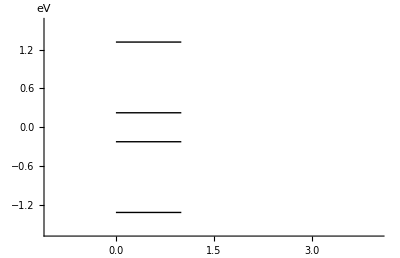

```mathematica
X[1,2]=PauliMatrix[1]⊗ PauliMatrix[1];
Hx=-ω1 Z[1] +-ω2 Z[2]+λ X[1,2];
Hx//MatrixForm
Eigensystem[Hx]//MatrixForm
HxCon=Simplify[Hx,{ω1==ω,ω2==ω}];
Eigensystem[Simplify[Hx,{ω1==ω,ω2==ω}]]//MatrixForm
energy=Simplify[Eigenvalues[Hx],{λ==.2,ω1==.6,ω2==.7}];
Graphics[{Inset[Style["(-ω1 - SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 - ω2), 2]] + ω2)/(λ SqrtBox[1 + SuperscriptBox[(FractionBox[ω1 + SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 - ω2), 2]] - ω2, λ]), 2]])01 + 1/(√(1 + SuperscriptBox[(FractionBox[ω1 + SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 - ω2), 2]] - ω2, λ]), 2]))10",10],{2.2,energy[[1]]}],Inset[Style["(-ω1 - ω2 - SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 + ω2), 2]])/(λ SqrtBox[1 + SuperscriptBox[(FractionBox[ω1 + ω2 + SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 + ω2), 2]], λ]), 2]])00 + 1/(√(1 + SuperscriptBox[(FractionBox[ω1 + ω2 + SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 + ω2), 2]], λ]), 2]))11",10],{2.2,energy[[3]]}],Inset[Style["(-ω1 + SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 - ω2), 2]] + ω2)/(λ SqrtBox[1 + SuperscriptBox[(FractionBox[-ω1 + SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 - ω2), 2]] + ω2, λ]), 2]])01 + 1/(√(1 + SuperscriptBox[(FractionBox[-ω1 + SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 - ω2), 2]] + ω2, λ]), 2]))10",10],{2.2,energy[[2]]}],Inset[Style["(-ω1 - ω2 + SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 + ω2), 2]])/(λ SqrtBox[1 + SuperscriptBox[(FractionBox[ω1 + ω2 - SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 + ω2), 2]], λ]), 2]])00 + 1/(√(1 + SuperscriptBox[(FractionBox[ω1 + ω2 - SqrtBox[SuperscriptBox[λ, 2] + SuperscriptBox[(ω1 + ω2), 2]], λ]), 2]))11",10],{2.2,energy[[4]]}],
Table[Line[{{0,energy[[i]]},{1,energy[[i]]}}],{i,1,4}]},
PlotRange->{{-1,4},{Min[energy]-.3,Max[energy]+.3}},
Axes->{False,True},
AxesLabel->eV]
```

```mathematica
PlotEnergy[H_,a_,b_,c_]:=Plot[Simplify[Eigenvalues[H],{λ==c,ω1==a,ω2==b}],{x,-1,1},PlotRange->All];
EngergyGaps[H_,a_,b_,c_]:=Block[{λ=c,ω1=a,ω2=b},{
{{1,3},(Eigenvalues[H][[1]]-Eigenvalues[H][[3]])},
{{1,4},(Eigenvalues[H][[1]]-Eigenvalues[H][[4]])},
{{2,4},(Eigenvalues[H][[2]]-Eigenvalues[H][[4]])},
{{2,3},(Eigenvalues[H][[2]]-Eigenvalues[H][[3]])},
{{1,2},(Eigenvalues[H][[1]]-Eigenvalues[H][[2]])},
{{3,4},(Eigenvalues[H][[3]]-Eigenvalues[H][[4]])}}
]//MatrixForm
waveFuction[a_,b_,c_,α1_,α2_,α3_,α4_]:=Simplify[(α1 orthonormalBasis[[1]]+α2 orthonormalBasis[[2]]+α3 orthonormalBasis[[3]]+α4 orthonormalBasis[[4]])/Sqrt[α1^2+α2^2+α3^2+α4^2],{λ ==c,ω1==a,ω2==b}];
orthogonalBasis=Eigenvectors[Hx];
orthonormalBasis=Simplify[Table[Normalize[orthogonalBasis[[i]]],{i,1,4}],Assumptions->{λ∈Reals,ω1∈Reals,ω2∈Reals}];
orthogonalBasis//MatrixForm
```

(0 | -(ω1-ω2+√(λ^2+ω1^2-2 ω1 ω2+ω2^2))/λ | 1 | 0
0 | -(ω1-ω2-√(λ^2+ω1^2-2 ω1 ω2+ω2^2))/λ | 1 | 0
-(ω1+ω2+√(λ^2+ω1^2+2 ω1 ω2+ω2^2))/λ | 0 | 0 | 1
-(ω1+ω2-√(λ^2+ω1^2+2 ω1 ω2+ω2^2))/λ | 0 | 0 | 1)

```mathematica
Manipulate[ {PlotEnergy[Hx,a,b,c],waveFuction[a,b,c,α1,α2,α3,α4]}//MatrixForm,{{a,.000},0,100,.01},{{b,.000},0,100,.01},{{c,0.01},0,20,.01},{{α1,.01},0,1,.01},{{α2,.000},0,1,.01},{{α3,.000},0,1,.01},{{α4,.000},0,1,.01}]
Simplify[orthonormalBasis,Assumptions->{λ>0}]//MatrixForm
```

(0 | (-ω1-√(λ^2+(ω1-ω2)^2)+ω2)/(λ √(1+((ω1+√(λ^2+(ω1-ω2)^2)-ω2)^2)/λ^2)) | 1/(√(1+((ω1+√(λ^2+(ω1-ω2)^2)-ω2)^2)/λ^2)) | 0
0 | (-ω1+√(λ^2+(ω1-ω2)^2)+ω2)/(λ √(1+((-ω1+√(λ^2+(ω1-ω2)^2)+ω2)^2)/λ^2)) | 1/(√(1+((-ω1+√(λ^2+(ω1-ω2)^2)+ω2)^2)/λ^2)) | 0
(-ω1-ω2-√(λ^2+(ω1+ω2)^2))/(λ √(1+((ω1+ω2+√(λ^2+(ω1+ω2)^2))^2)/λ^2)) | 0 | 0 | 1/(√(1+((ω1+ω2+√(λ^2+(ω1+ω2)^2))^2)/λ^2))
(-ω1-ω2+√(λ^2+(ω1+ω2)^2))/(λ √(1+((ω1+ω2-√(λ^2+(ω1+ω2)^2))^2)/λ^2)) | 0 | 0 | 1/(√(1+((ω1+ω2-√(λ^2+(ω1+ω2)^2))^2)/λ^2)))

### Gate Applications with time-independent fields

Analytical Solution

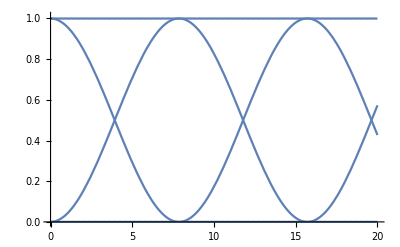

```mathematica
P=Eigenvectors[Hx];
Pinv=Inverse[Eigenvectors[Hx]];
Λ=DiagonalMatrix[Eigenvalues[Hx]];
U[c_,a_,b_,t_]:=Simplify[Pinv.MatrixExp[- I Λ t].P,{λ==c,ω1==a,ω2==b}];
PlotCoeffcients[c_,a_,b_,U_,ψ_]:=Block[{Ut=U[c,a,b,t].ψ},
f[t_]:=
Table[Norm[Ut[[i]]]^2,{i,1,4}];
Plot[f[t],{t,0,20},PlotRange->{0,1.01}]
];
PlotCoeffcients[.2,5,5,U,({{0}, {1}, {0}, {1}})]
```

Numerical solution

```mathematica
H0[t_]:=Hx;
Hp[t_]:=(Ω0 Cos[ω t]PauliMatrix[1])⊗IdentityMatrix[2];
U0[t_]:=MatrixExp[-I Hx t];
```

```mathematica
H1[t_]:=Simplify[H0[t]+(UnitStep[t-2]-UnitStep[t-6])Hp[t],{λ==1,ω1==5,ω2==5,ω==5,Ω0==8}];
H2[t_]:=Simplify[SuperDagger[U0[t]].Hp[t].U0[t],{λ==1,ω1==5,ω2==5,ω==5,Ω0==8}];
```

```mathematica
H2[6.]//Chop//MatrixForm
```

(0 | -0.196262-0.350258 ⅈ | -0.952226+0.674427 ⅈ | 0
-0.196262+0.350258 ⅈ | 0 | 0 | -0.952226+0.674427 ⅈ
-0.952226-0.674427 ⅈ | 0 | 0 | 0.196262+0.350258 ⅈ
0 | -0.952226-0.674427 ⅈ | 0.196262-0.350258 ⅈ | 0)

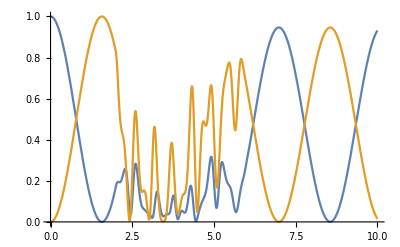

```mathematica
Sol=USolve[H1,IdentityMatrix[4],0,10,1];
Prob[t_,i_,j_]:=Abs[Sol[t][[i,j]]]^2;
Plot[{Prob[t,2,2],Prob[t,2,3]},{t,0,10},PlotRange->{0,1}]
```

```mathematica
PauliMatrix[1]⊗IdentityMatrix[2]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
Sol[6]
```

{{-0.687535-0.686763 ⅈ,-0.0898069+0.17559 ⅈ,0.110421-0.0464276 ⅈ,0.0484582+0.00789625 ⅈ},{0.0649005+0.0660162 ⅈ,-0.538633-0.0249556 ⅈ,0.00463634-0.80993 ⅈ,0.180082-0.110662 ⅈ},{-0.180082-0.110662 ⅈ,-0.00463634-0.80993 ⅈ,-0.538633+0.0249556 ⅈ,0.0649005-0.0660162 ⅈ},{-0.0484582+0.00789625 ⅈ,-0.110421-0.0464276 ⅈ,-0.0898069-0.17559 ⅈ,-0.687535+0.686763 ⅈ}}

```mathematica
Manipulate[{Sol[t].({{1}, {0}, {0}, {0}})/Sqrt[2]//Chop//MatrixForm},{{t,.000},0,5,.01}]
```

```mathematica
PauliMatrix[3].PauliMatrix[1].PauliMatrix[3]-PauliMatrix[2]//MatrixForm
```

(0 | -1+ⅈ
-1-ⅈ | 0)

```mathematica
Manipulate[{{Sol[t].({{1}, {0}, {0}, {0}})//MatrixForm},{Sol[t].eigvecs[[1]],Sol[t].eigvecs[[2]],Sol[t].eigvecs[[3]],Sol[t].eigvecs[[4]]}*Exp[-I ArcTan[Im[(Sol[t].eigvecs[[1]])[[2]]]/Re[(Sol[t].eigvecs[[1]])[[2]]]]]}//Chop//MatrixForm,{{t,.000},0,5,.01}]
```

```mathematica
Sol[0].eigvecs[[1]]//Chop
Hp[t_]:=-50 Z[1];
SolPulse=USolve[Hp,IdentityMatrix[4],0,10,1];
Manipulate[Tr[(SolPulse[t]-Z[1])]//Chop,{{t,.0000000},0,1,.0001}]
```

Part::partd: Part specification eigvecs⟦1⟧ is longer than depth of object.

{{1.,0,0,0},{0,1.,0,0},{0,0,1.,0},{0,0,0,1.}}.eigvecs⟦1⟧

```mathematica
FindMaximum[1/Tr[SolPulse[t]],t]
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{1.80287×10^10,{t→0.84823}}

```mathematica
Prob2[t_,i_,j_]:=Abs[UTotal[t][[i,j]]]^2;
Block[{
Δt=Pi/100,t0=4},
Hp[t_]:=H0[t]-45 Z[1];
U1=USolve[H0,IdentityMatrix[4],0,t0,1];
U2=USolve[Hp,IdentityMatrix[4],t0,t0+Δt,1];
U3=USolve[H0,U2[t0+Δt],t0+Δt,10,1];
UTotal[t_]:=Piecewise[{{U1[t],t<t0},{U2[t],t≥t0&&t<t0+Δt},{U3[t],t>=t0+Δt}}];
Plot[{Prob2[t,2,2],Prob2[t,3,3]},{t,0,10},PlotRange->{0,1}];
U2[t0+Δt]Exp[I 3 Pi/2]//Chop//MatrixForm;
Fidelity[U2[t0+Δt]Exp[I 3 Pi/2],Z[1]]
]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at BasicFunctions`Private`tSol == 0..

ReplaceAll::reps: {NDSolve[{ⅈ BasicFunctions`Private`USol'[BasicFunctions`Private`tSol]=={{Plus[«2»],0,0,λ},{0,Plus[«2»],λ,0},{0,λ,Plus[«2»],0},{λ,0,0,Plus[«2»]}}.BasicFunctions`Private`USol[BasicFunctions`Private`tSol],BasicFunctions`Private`USol[0]=={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}},BasicFunctions`Private`USol,{BasicFunctions`Private`tSol,0,4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at BasicFunctions`Private`tSol == 4..

ReplaceAll::reps: {NDSolve[{ⅈ BasicFunctions`Private`USol'[BasicFunctions`Private`tSol]=={{Plus[«3»],0,0,λ},{0,Plus[«3»],λ,0},{0,λ,Plus[«3»],0},{λ,0,0,Plus[«3»]}}.BasicFunctions`Private`USol[BasicFunctions`Private`tSol],BasicFunctions`Private`USol[4]=={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}},BasicFunctions`Private`USol,{BasicFunctions`Private`tSol,4,4+π/100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {ⅈ BasicFunctions`Private`USol'[BasicFunctions`Private`tSol]=={{-ω1-ω2,0,0,λ},{0,-ω1+ω2,λ,0},{0,λ,ω1-ω2,0},{λ,0,0,ω1+ω2}}.BasicFunctions`Private`USol[BasicFunctions`Private`tSol],True}.

ReplaceAll::reps: {NDSolve[{ⅈ BasicFunctions`Private`USol'[BasicFunctions`Private`tSol]=={{Plus[«2»],0,0,λ},{0,Plus[«2»],λ,0},{0,λ,Plus[«2»],0},{λ,0,0,Plus[«2»]}}.BasicFunctions`Private`USol[BasicFunctions`Private`tSol],True},BasicFunctions`Private`USol,{BasicFunctions`Private`tSol,4+π/100,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of BasicFunctions`Private`USol[0.000204286] does not exist.

Part::partw: Part 2 of BasicFunctions`Private`USol[0.204286] does not exist.

Part::partw: Part 2 of BasicFunctions`Private`USol[0.408368] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Fidelity[-ⅈ BasicFunctions`Private`USol[4+π/100],{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}}]